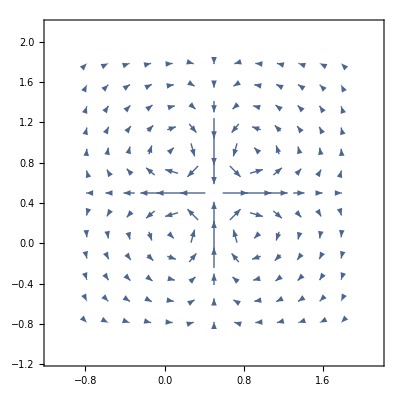

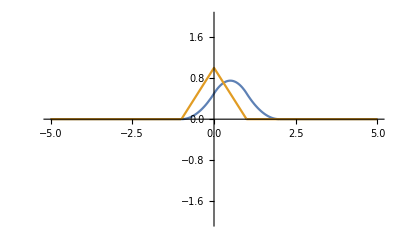

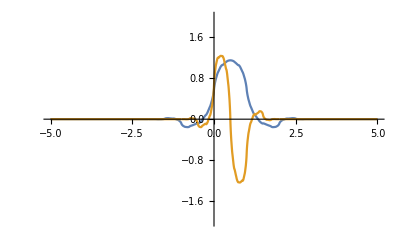

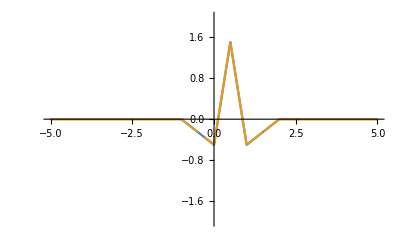

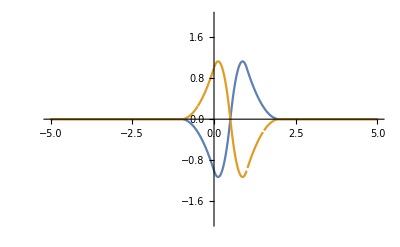

DiscreteWaveletTransform::bbdwave: The specification BiorthogonalSplineWavelet[1, 3]\ BiorthogonalSplineWavelet[2, 2] is not a valid wavelet specification recognized by the system.

DiscreteWaveletTransform::bdwave: The wavelet specification BiorthogonalSplineWavelet[1, 3]\ BiorthogonalSplineWavelet[2, 2] cannot be used to perform DiscreteWaveletTransform.

DiscreteWaveletTransform[-Graphics-,BiorthogonalSplineWavelet[1,3] BiorthogonalSplineWavelet[2,2],3]

InverseWaveletTransform::dwd: First argument … to InverseWaveletTransform should be a DiscreteWaveletData object.

InverseWaveletTransform[DiscreteWaveletTransform[-Graphics-,BiorthogonalSplineWavelet[1,3] BiorthogonalSplineWavelet[2,2],3]]

DiscreteWaveletTransform[-Graphics-,BiorthogonalSplineWavelet[1,3] BiorthogonalSplineWavelet[2,2],3][All,Image]

```mathematica
Subscript[Phi, 0][x_]=WaveletPhi[BiorthogonalSplineWavelet[2,2],x,"Dual"];
Subscript[PhiDual, 0][x_]=WaveletPhi[BiorthogonalSplineWavelet[2,2],x];
Subscript[Psi, 0][x_] = WaveletPsi[BiorthogonalSplineWavelet[2,2],x,"Dual"];
Subscript[PsiDual, 0][x_] = WaveletPsi[BiorthogonalSplineWavelet[2,2],x];
Subscript[Phi, 1][x_]=WaveletPhi[BiorthogonalSplineWavelet[3,1],x,"Dual"];
Subscript[PhiDual, 1][x_]=WaveletPhi[BiorthogonalSplineWavelet[1,3],x];
Subscript[Psi, 1][x_] = -WaveletPsi[BiorthogonalSplineWavelet[3,1],x,"Dual"];
Subscript[PsiDual, 1][x_] = WaveletPsi[BiorthogonalSplineWavelet[1,3],x];
BigPhi[x_,y_] = {Subscript[Phi, 1][x](Subscript[Phi, 0][y]-Subscript[Phi, 0][y-1]),-(Subscript[Phi, 0][x]-Subscript[Phi, 0][x-1])Subscript[Phi, 1][y]};
Subscript[BigPsi, 1,0][x_,y_]={-1/4.0*Subscript[Psi, 1][x](Subscript[Phi, 0][y]-Subscript[Phi, 0][y-1]),Subscript[Psi, 0][x]Subscript[Phi, 1][y]};
Subscript[BigPsi, 0,1][x_,y_]={Subscript[Phi, 1][x]Subscript[Psi, 0][y],-1/4.0*(Subscript[Phi, 0][x]-Subscript[Phi, 0][x-1])Subscript[Psi, 1][y]};
Subscript[BigPsi, 1,1][x_,y_]={Subscript[Psi, 1][x]Subscript[Psi, 0][y],-Subscript[Psi, 0][x]Subscript[Psi, 1][y]};

VectorPlot[Subscript[BigPsi, 1,1][x,y],{x,-1,2},{y,-1,2}]
Plot[{Subscript[Phi, 1][x],Subscript[Phi, 0][x]},{x,-5,5},PlotRange->2]
Plot[{Subscript[PhiDual, 1][x],Subscript[PsiDual, 1][x]},{x,-5,5},PlotRange->2]
Plot[{Subscript[Psi, 0][x],Subscript[Phi, 0][2x+1]/-4+Subscript[Phi, 0][2x]/-2+Subscript[Phi, 0][2x-1]/2*3+Subscript[Phi, 0][2x-2]/-2+Subscript[Phi, 0][2x-3]/-4},{x,-5,5},PlotRange->2]
Plot[{Subscript[Psi, 1][x],Subscript[Phi, 1][2x+1]/2+Subscript[Phi, 1][2x]/2*3-Subscript[Phi, 1][2x-1]/2*3-Subscript[Phi, 1][2x-2]/2},{x,-5,5},PlotRange->2]
dwd=DiscreteWaveletTransform[-Graphics-,BiorthogonalSplineWavelet[1,3]BiorthogonalSplineWavelet[2,2],3]
InverseWaveletTransform[dwd]
dwd[All,"Image"]
```